ricorda che devi corregere con alpha non hardcoded, qui non é ancora fatto

```mathematica
file=Import["/Users/pagani/mg5_3.5/mupemtomupemtt_v2/HTML/plottaprova/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_plottaprova/MadAnalysis5job_0/Histograms/histos.saf","Table"];
nhisto=0;
namehisto=Table[0,{j,1,100}];
positions=Table[0,{j,1,100}];
Do[
If[file[[i]]=={"<Histo>"}, 
nhisto=nhisto+1;
namehisto[[nhisto]]=file[[i+2]];
positions[[nhisto]]=i];
     ,{i,1,Length[file]}];
namehisto=Take[namehisto,nhisto];
positions=Take[positions,nhisto];
Do[(*Print[file[[ positions[[i]]+4 ]] ];*)binning[i]=file[[ positions[[i]]+4 ]];passo[i]=(binning[i][[3]]-binning[i][[2]])/binning[i][[1]],{i,1,nhisto}];
 Do[histo[i]=Table[{binning[i][[2]]+(j-1)passo[i],file[[positions[[i]]+18+j ,1 ]]},{j,0,binning[i][[1]]+1}],{i,1,nhisto}]
```

```mathematica
Estrai[filename_,histo_,namehisto_,nhisto_]:=Module[{file,positions,binning},
histo=.;
namehisto=.;
nhisto=.;
file=Import[filename,"Table"];
nhisto=0;
namehisto=Table[0,{j,1,100}];
positions=Table[0,{j,1,100}];
Do[
If[file[[i]]=={"<Histo>"}, 
nhisto=nhisto+1;
namehisto[[nhisto]]=file[[i+2]];
positions[[nhisto]]=i];
     ,{i,1,Length[file]}];
namehisto=Take[namehisto,nhisto];
positions=Take[positions,nhisto];
Do[(*Print[file[[ positions[[i]]+4 ]] ];*)binning[i]=file[[ positions[[i]]+4 ]];passo[i]=(binning[i][[3]]-binning[i][[2]])/binning[i][[1]],{i,1,nhisto}];
 Do[histo[i]=Table[{binning[i][[2]]+(j-1)passo[i],file[[positions[[i]]+18+j ,1 ]]},{j,0,binning[i][[1]]+1}],{i,1,nhisto}]
]
```

```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
nomicartelle=Import["/Users/pagani/mg5_3.5/lista_cartellemumumassive.dat","List"]
quantities={aaWW,muaWW,mua,aa,mumu,total,nocutsmuaWW,OPmuaWW,OPmua,OPaa,OPmumu,OPtotal,OPnocutsmuaWW}
```

{aatottformuu,altottl,mupemtomupemtt,mupemtomupemtt_v0,mupemtomupemtt_v2,nocut_mupemtomupemtt,nocuts_altottl,onlyphoton_altottl,onlyphoton_mupemtomupemtt,onlyphoton_mupemtomupemtt_v0,onlyphoton_mupemtomupemtt_v2,onlyphoton_nocut_mupemtomupemtt,onlyphoton_nocuts_altottl}

{aaWW,muaWW,mua,aa,mumu,total,nocutsmuaWW,OPmuaWW,OPmua,OPaa,OPmumu,OPtotal,OPnocutsmuaWW}

checkEQeightyfive

_m1

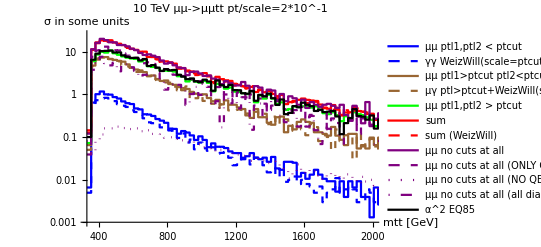

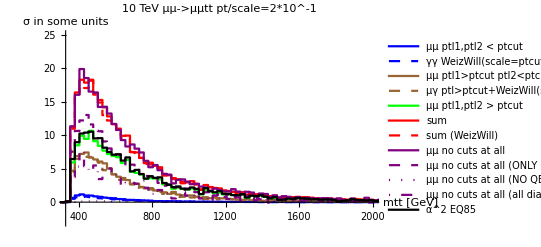

/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d0.pdf

/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d0.pdf

```mathematica
namerun="distr2ndtry";
namerun="checkEQeightyfive"


inputptcutscale=-1;



ptcutscale=ToString[inputptcutscale];
ptcutscalev2=ToString[inputptcutscale];
If[inputptcutscale<0,ptcutscalev2="_m"<>ToString[Abs[inputptcutscale]]]


listaistogrammi=Table[0,{i,1,Length[nomicartelle]}];
Do[
nomi=.;
nhistos=.;
inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscalev2<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf";

(*If[i===6 || i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscalev2<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];

If[ i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscalev2<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];*)


Estrai[inputname,quantities[[i]],nomi,nhistos],
{i,1,Length[nomicartelle]}];


Estrai["/Users/pagani/mg5_3.5/"<>"mupemtottbar_nophotons"<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscalev2<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf",NPtotal,nomiNP,nhistosNP]
nomiNP=.;
nhistosNP=.;

numberplot=11;

unisci[x_]:=joinbin[x,5];

summed=sum[mumu[numberplot],sum[aa[numberplot],mua[numberplot]]];
summedWWa=sum[mumu[numberplot],sum[aaWW[numberplot],muaWW[numberplot]]];
ZPtotal=diff[total[numberplot],sum[NPtotal[numberplot],OPtotal[numberplot]]];

RHS2nd82=diff[mua[numberplot], muaWW[numberplot]];
RHS3rd=diff[aa[numberplot], aaWW[numberplot]];
ddelta2S= diff[nocutsmuaWW[numberplot],coeff[aaWW[numberplot],2]];
RHS2nd83=diff[mua[numberplot], ddelta2S];
alpha2EQ85=sum[sum[mumu[numberplot],RHS2nd83],RHS3rd];


logplotmtt=ListLogPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]],unisci[OPtotal[numberplot]],unisci[NPtotal[numberplot]],unisci[ZPtotal],unisci[alpha2EQ85]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","μμ no cuts at all (ONLY QED)","μμ no cuts at all (NO QED)","μμ no cuts at all (all diag -(only QED + NO QED))","α^2 EQ85"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,{Purple,Dashed},{Purple,Dotted},{Purple,DotDashed},Black},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

plotmtt=ListPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]],unisci[OPtotal[numberplot]],unisci[NPtotal[numberplot]],unisci[ZPtotal],unisci[alpha2EQ85]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","μμ no cuts at all (ONLY QED)","μμ no cuts at all (NO QED)","μμ no cuts at all (all diag -(only QED + NO QED))","α^2 EQ85"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,{Purple,Dashed},{Purple,Dotted},{Purple,DotDashed},Black},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d"<>ToString[ptcutscale]<>".pdf",logplotmtt];
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d"<>ToString[ptcutscale]<>".pdf",plotmtt];

"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d0.pdf"
"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d0.pdf"
```

```mathematica
nomi
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_M},{14_DELTAR},{15_DELTAR},{16_DELTAR}}

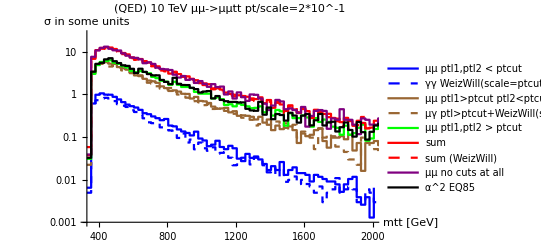

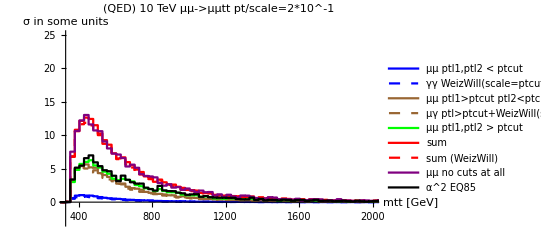

```mathematica
OPsummed=sum[OPmumu[numberplot],sum[OPaa[numberplot],OPmua[numberplot]]];
OPsummedWWa=sum[OPmumu[numberplot],sum[aaWW[numberplot],OPmuaWW[numberplot]]];

OPRHS2nd82=diff[OPmua[numberplot], OPmuaWW[numberplot]];
OPRHS3rd=diff[OPaa[numberplot], aaWW[numberplot]];
OPddelta2S= diff[OPnocutsmuaWW[numberplot],coeff[aaWW[numberplot],2]];
OPRHS2nd83=diff[OPmua[numberplot], OPddelta2S];
OPalpha2EQ85=sum[sum[OPmumu[numberplot],OPRHS2nd83],OPRHS3rd];

OPlogplotmtt=ListLogPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]],unisci[OPalpha2EQ85]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","α^2 EQ85"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,Black},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

OPplotmtt=ListPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]],unisci[OPalpha2EQ85]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","α^2 EQ85"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,Black},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]
```

```mathematica
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/OPlogplotmtt10d"<>ToString[ptcutscale]<>".pdf",OPlogplotmtt];
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/OPplotmtt10d"<>ToString[ptcutscale]<>".pdf",OPplotmtt];
```

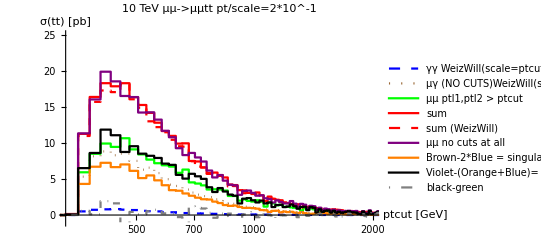

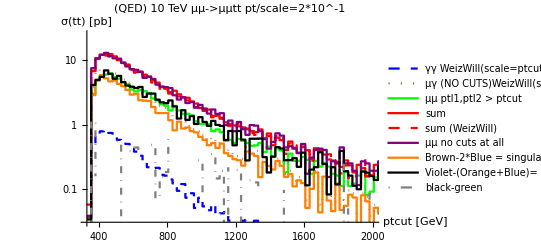

```mathematica
muaWWminus2aa=diff[nocutsmuaWW[numberplot],coeff[aaWW[numberplot],2]];
nodiv=diff[total[numberplot],sum[aaWW[numberplot],muaWWminus2aa]];
OPmuaWWminus2aa=diff[OPnocutsmuaWW[numberplot],coeff[aaWW[numberplot],2]];
OPnodiv=diff[OPtotal[numberplot],sum[aaWW[numberplot],OPmuaWWminus2aa]];


ListLogLinearPlot[{unisci[aaWW[numberplot]],unisci[nocutsmuaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]],unisci[muaWWminus2aa],unisci[nodiv],unisci[diff[nodiv,mumu[numberplot]]]},Joined->True,InterpolationOrder->0,PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale],AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{ "γγ WeizWill(scale=ptcut)","μγ (NO CUTS)WeizWill(scale=ptcut)","μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","Brown-2*Blue = singular div.", "Violet-(Orange+Blue)= μμ no cuts at all - (singular + double div.) ", "black-green"},PlotStyle->{{Blue,Dashed},{Brown,Dotted},Green,Red,{Red,Dashed},Purple,Orange,Black,{Gray,DotDashed}},PlotRange->{{330,2000},{-1,25}}]

ListLogPlot[{unisci[aaWW[numberplot]],unisci[OPnocutsmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]],unisci[OPmuaWWminus2aa],unisci[OPnodiv],unisci[diff[OPnodiv,OPmumu[numberplot]]]},Joined->True,InterpolationOrder->0,PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale],AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{ "γγ WeizWill(scale=ptcut)","μγ (NO CUTS)WeizWill(scale=ptcut)","μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","Brown-2*Blue = singular div.", "Violet-(Orange+Blue)= μμ no cuts at all - (singular + double div.) ", "black-green"},PlotStyle->{{Blue,Dashed},{Brown,Dotted},Green,Red,{Red,Dashed},Purple,Orange,Black,{Gray,DotDashed}},PlotRange->{{330,2000},{-1,25}}]
```